#### Find the closest path between two elastic maps INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb, then this notebook Variables to change: Tmat, dt, RangeSigma

#### choose Tmat

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatBrown;
```

```mathematica
Tmat=TmatIgel;
```

#### check that it’s symmetric, display info

```mathematica
Tmat==Transpose[Tmat]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

#### Find closest T to ISO

```mathematica
WantDetails="WantDetails";
```

```mathematica
OutputFor[Tmat,ISO]
```

```mathematica
betaISO =βTinitial[Tmat,ISO]/Degree  (* AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree *)
TISO =ProjToVSigOfU[Tmat,id,ISO];  (* Closest[Tmat,ISO] *)
MatrixForm[TISO]
```

#### Matrix norms (not used, but worth thinking about)

```mathematica
Ntriv =Norm[Tmat,Frobenius]
Niso =Norm[TISO,Frobenius]
Norm[TISO/Niso,Frobenius]
Norm[Ntriv/Ntriv,Frobenius]
```

#### check: the angle does not depend on the size of the T

```mathematica
AngleMatrix[Tmat,TISO]/Degree
AngleMatrix[Tmat/Ntriv,TISO/Niso]/Degree
```

#### Choose Tmat1 and Tmat2

```mathematica
Tmat1 =TISO;
Tmat2 =Tmat;
```

#### KEY FUNCTION

```mathematica
TT[t_,Tmat1_,Tmat2_]:=(1-t) Tmat1+t Tmat2
```

#### check endpoints

```mathematica
MatrixForm[Tmat1]
MatrixForm[TT[0,Tmat1,Tmat2]]
MatrixForm[Tmat2]
MatrixForm[TT[1,Tmat1,Tmat2]]
```

#### t values to use

```mathematica
t1 = 1; t2=1.1;dt =0.01;   (* Igel -- show that t > 1 *)
t1 = 0; t2=1;
dt = 0.1;
dt =0.5;
Ranget=Range[t1,t2,dt]
```

#### Display the set of Tmats as BB and as Voigt

```mathematica
(Print["t = ",# ]; PrintVoigt[TT[#,Tmat1,Tmat2]])&/@Ranget
```

## Aside: Choose an orientation for all the balls based on the closest XISO (or whatever you want).

#### commands copied from LatticeOfClosestMaps.nb Display the set of REORIENTED Tmats as BB and as Voigt

```mathematica
(* WantDetails="WantDetails";
OutputFor[Tmat,XISO]
MatrixForm[UT[Tmat,XISO]]
MatrixForm[Closest[Tmat,XISO]]
OutputFor[Closest[Tmat,XISO],XISO]
Ux=IdentityMatrix[3];
(* Ux=UT[Closest[Tmat,XISO],XISO]; *)
MatrixForm[Ux]
Ubarx=MatrixUbar[Ux];
MatrixForm[Chop[Ubarx,.0001]]
(Print["t = ",# ]; PrintVoigt[Transpose[Ubarx].TT[#,Tmat1,Tmat2].Ubarx])&/@Ranget *)
```

## Proceed with the original input Tmat (angles among maps will be unchanged) Preliminaries for beta curves

#### Set of Sigmas to use

```mathematica
RangeSigma={TRIV,MONO,TRIG,ORTH,TET,CUBE,XISO,ISO};
```

```mathematica
RangeSigma={ORTH,TET};
```

#### Example of plotting two sets of points on one plot.

```mathematica
f[t_,Sigma_]:=t/2
```

```mathematica
Graphics[{PointSize[.02],
Table[Point[{t,0}],                    {t,.2,.8,.2}],
Table[Point[{t,f[t,XISO]}],{t,.2,.8,.2}],
Table[Point[{t,f[t,ORTH]}],{t,.2,.8,.2}]},Axes->True,AxesOrigin->{0,0}]
```

#### Example: Closest to MONO for t=0.2

```mathematica
Ttest =TT[.2,Tmat1,Tmat2];
MatrixForm[Ttest]
OutputFor[Ttest,MONO]
```

#### This is the rotation from the minimization.

```mathematica
(* UT[Tmat,Σ] *)
```

#### This is the corresponding elastic map.

```mathematica
(* MatrixForm[ProjToVSigOfU[Tmat,UT[Tmat,Σ],Σ]] *)
```

#### This command is in the common_funs file.

```mathematica
(* Closest[Tmat_,Sigma_]:=ProjToVSigOfU[Tmat,UT[Tmat,Sigma],Sigma]; *)
```

#### This is the angle between Tmat and the closest Sigma map.

```mathematica
(* AngleMatrix[Tmat,Closest[Tmat,Sigma]] *)
```

#### This is the first matrix in OutputFor

```mathematica
MatrixForm[UT[Ttest,MONO]]
```

#### This is the last matrix in OutputFor (Closest[Tmat,Sigma] is defined in common_funs.nb)

```mathematica
MatrixForm[Closest[Ttest,MONO]]
```

#### These are the βs in OutputFor

```mathematica
AngleMatrix[Ttest,Closest[Ttest,MONO]]/Degree
```

## Calculate distance to each symmetry class

```mathematica
WantDetails="NoWantDetails";
```

#### KEY COMMAND: OutputFor performs the key calculations (minimizations)

```mathematica
(* Table[OutputFor[TT[t,Tmat1,Tmat2],#]&/@RangeSigma,{t,t1,t2,dt}] *)
```

```mathematica
Do[(Print["t = ",t];
OutputFor[TT[t,Tmat1,Tmat2],#])&/@RangeSigma,{t,t1,t2,dt}]
```

#### Angle between Tmat and the closest-Sigma to Tmat

```mathematica
f[Tmat_,Sigma_]:=MakeReal[AngleMatrix[Tmat,Closest[Tmat,Sigma]]/Degree];
```

#### Plot all the beta curves together. (With the Closest maps pre-saved, the plotting should be quick.)

```mathematica
RangeSigma
```

```mathematica
line[Sigma_]:=Line[{#,f[TT[#,Tmat1,Tmat2],Sigma]}&/@Ranget];
```

```mathematica
Graphics[{PointSize[.02],
line/@RangeSigma,
Text[Style[SequenceForm[#," (",Round[f[TT[t2,Tmat1,Tmat2],#],0.01],")"],13],{t2+.03,f[TT[t2,Tmat1,Tmat2],#]},{-1,0}]&/@RangeSigma},Axes->True,AxesOrigin->{t1,0},AspectRatio->1]
```

#### This fancier version with colored dots will require having run the full set for RangeSigma. It will generate figures like the ones saved below.

```mathematica
(* Graphics[{PointSize[.02],
line/@RangeSigma,
{ColorData["Rainbow"][0/6],Point[{#,f[TT[#,Tmat1,Tmat2],MONO]}]&/@Ranget},
{ColorData["Rainbow"][1/6],Point[{#,f[TT[#,Tmat1,Tmat2],ORTH]}]&/@Ranget},
{ColorData["Rainbow"][2/6],Point[{#,f[TT[#,Tmat1,Tmat2],  TET]}]&/@Ranget},
{ColorData["Rainbow"][3/6],Point[{#,f[TT[#,Tmat1,Tmat2],TRIG]}]&/@Ranget},
{ColorData["Rainbow"][4/6],Point[{#,f[TT[#,Tmat1,Tmat2],XISO]}]&/@Ranget},
{ColorData["Rainbow"][5/6],Point[{#,f[TT[#,Tmat1,Tmat2],CUBE]}]&/@Ranget},
{ColorData["Rainbow"][6/6],Point[{#,f[TT[#,Tmat1,Tmat2],  ISO]}]&/@Ranget},
Point[{#,0}]&/@Ranget,Point[{1,0}],
Text[Style[#,13],{t2+.03,f[TT[t2,Tmat1,Tmat2],#]},{-1,0}]&/@RangeSigma},Axes->True,AxesOrigin->{t1,0},AspectRatio->1,ImageSize->500] *)
```

## For reference

#### Igel: dt = 0.5, RangeSigma = {ORTH, TET}

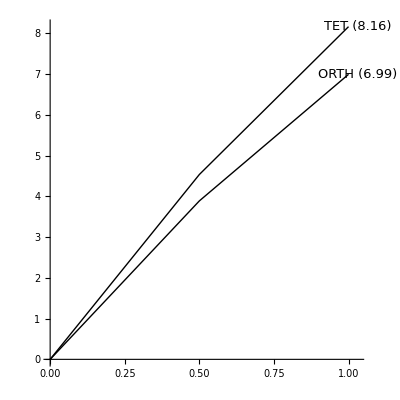

#### Igel: dt = 0.1, RangeSigma = all

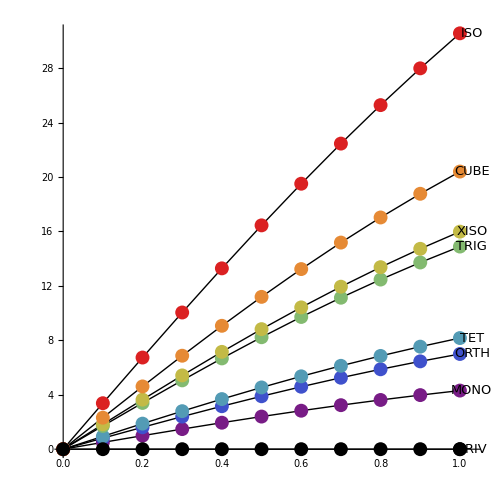

#### TmatMar17: dt = 0.1, RangeSigma = all

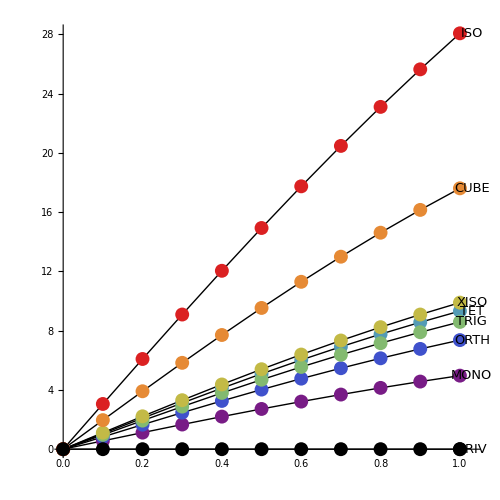

#### TmatBrown: dt = 0.1, RangeSigma = all